## Invoice

Getting the data from the invoice.csv file

We import the Data from the invoice.csv file,

Take the headers from the first row of the csv file

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) invoice

```mathematica
csv=Import[FileNameJoin[{NotebookDirectory[],"data_code","invoice.csv"}]];
headers=First[csv];
assoc=Association[Thread[headers->#]]&/@Rest[csv];
invoice=Dataset[assoc];
```

Getting the data from the items.csv

We import the Data from the item.csv file,

Take the headers from the first row of the csv file and call it headersItem

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) item

```mathematica
csvItem=Import[FileNameJoin[{NotebookDirectory[],"data_code","item.csv"}]];
headersItem=First[csvItem];
assocItem=Association[Thread[headersItem->#]]&/@Rest[csvItem];
item=Dataset[assocItem];
```

Here we look at the lengths of the datasets

```mathematica
{Length[invoice],Length[item]}
```

{930508,4166}

and the names of the headers for each

```mathematica
headers
```

{Invoice_id,Date,Item_id,Vendor_id,Vendor_Name,Store_id,Store_Name,Address,City_Name,Zip_Code,County_id,County_Name,Bottles_Sold}

```mathematica
headersItem
```

{Item_id,Item_Description,Category,Pack,Bottle_Volume_ml,Bottle_Cost,Bottle_Retail_Price}

we see that they share a Item_Id tag so we would like to merge them into one, Using JoinAccross.  This takes a few seconds.

```mathematica
itemInvoice=JoinAcross[invoice,item,"Item_id"];
```

The following is an example on how to add a new column keyed under “Purchase_Cost” obtained from the product of the “Bottles_Sold” value with the “Bottle_Retail_Price”.

```mathematica
RandomChoice[itemInvoice]/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]
```

We can do the above to the whole dataset

```mathematica
withPurchaseCost=(itemInvoice/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]);
```

```mathematica
RandomChoice[withPurchaseCost]
```

```mathematica
withPurchaseCost[Counts,"Item_Description"]["Miku's Leek Juice"]
```

9

```mathematica
Length[withPurchaseCost]
```

930508

```mathematica
withPurchaseCost[Counts,"Date"]
```

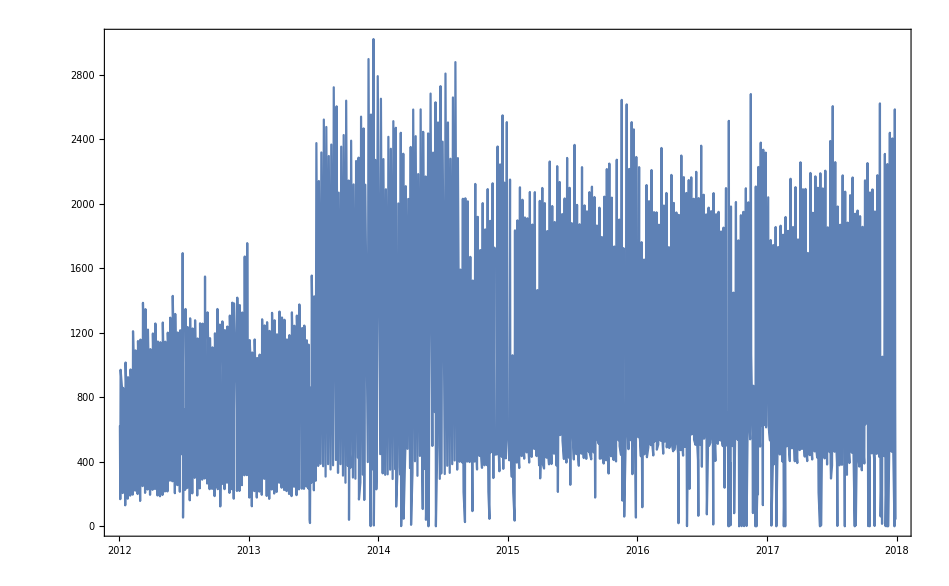

```mathematica
DateListPlot[withPurchaseCost[Counts,"Date"]]
```

```mathematica
JoinAcross[{<|"a"->1,"b"->2|>,<|"a"->2,"b"->2|>},{<|"a"->1,"c"->3|>,<|"a"->1,"c"->1|>,<|"a"->2,"c"->2|>},"a"]
```

{<|a→1,b→2,c→3|>,<|a→1,b→2,c→1|>,<|a→2,b→2,c→2|>}

```mathematica
JoinAcross[Dataset[{<|"a"->1,"b"->2|>,<|"a"->2,"b"->2|>}],Dataset[{<|"a"->1,"c"->3|>,<|"a"->1,"c"->1|>,<|"a"->2,"c"->2|>}],"a"]
```

```mathematica
invoice[Counts,"Item_id"]
```

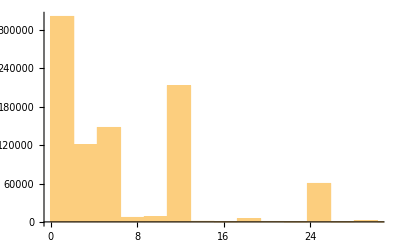

```mathematica
invoice[Histogram,"Bottles_Sold"]
```

```mathematica
invoice[Max,"Bottles_Sold"]
```

2160

```mathematica
invoice[Min,"Bottles_Sold"]
```

0

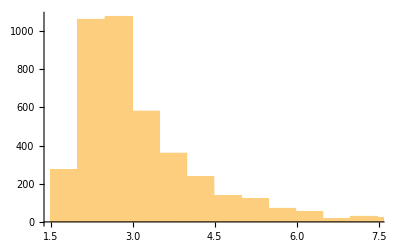

```mathematica
item[Histogram,"Bottle_Cost"]
```

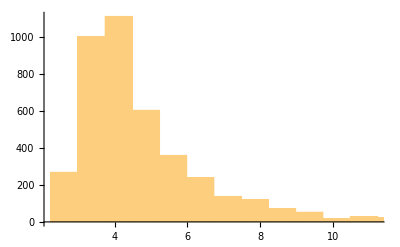

```mathematica
item[Histogram,"Bottle_Retail_Price"]
```

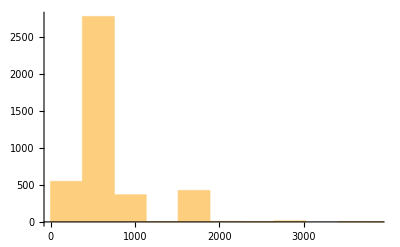

```mathematica
item[Histogram,"Bottle_Volume_ml"]
```

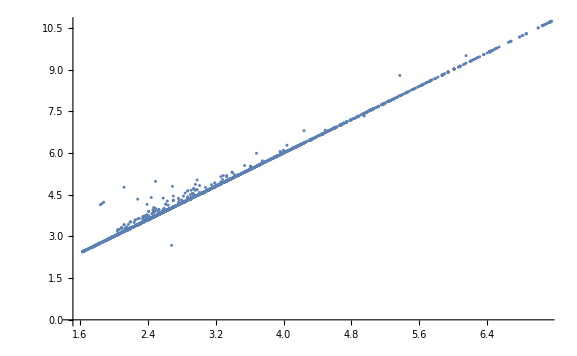

```mathematica
item[ListPlot,{"Bottle_Cost","Bottle_Retail_Price"}]
```

```mathematica
$ImportFormats
```

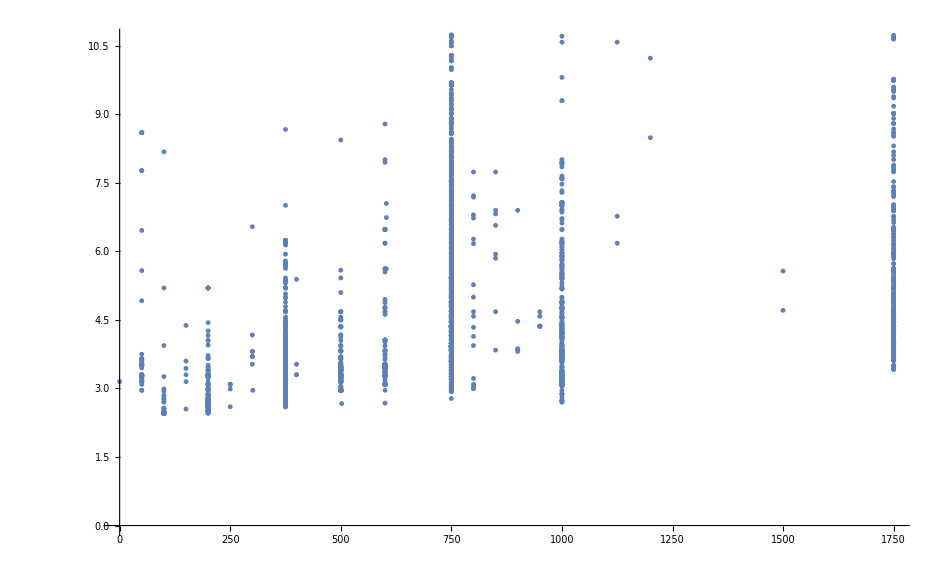

```mathematica
item[ListPlot,{"Bottle_Volume_ml","Bottle_Retail_Price"}]
```

```mathematica
item[Max,"Bottle_Volume_ml"]
```

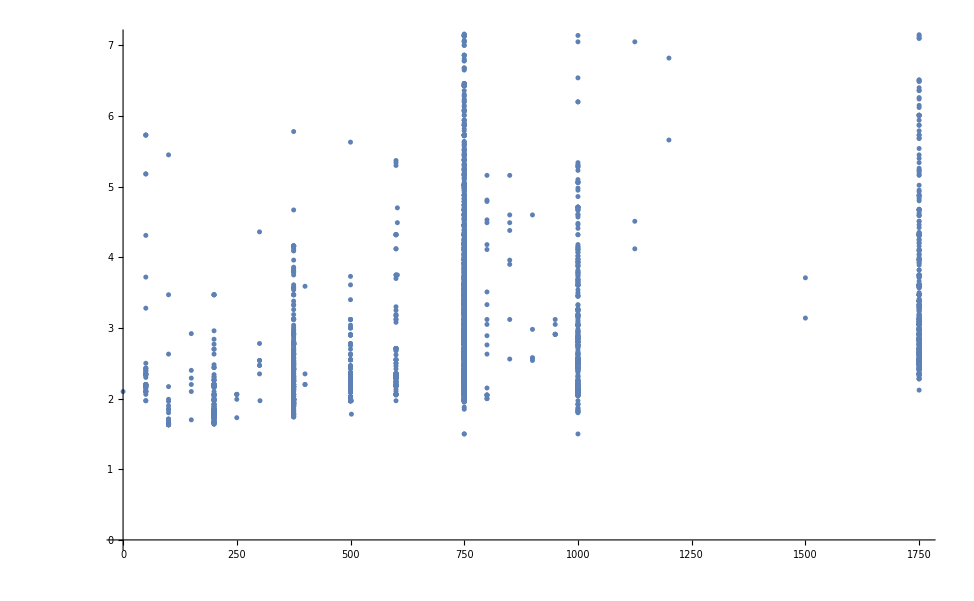

```mathematica
item[ListPlot,{"Bottle_Volume_ml","Bottle_Cost"}]
```

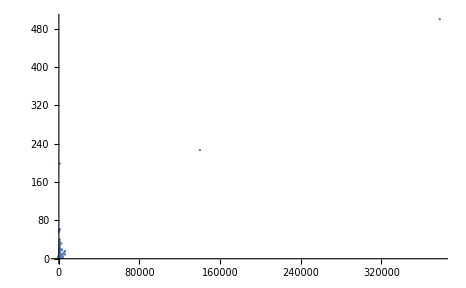

```mathematica
ListPlot[item[All,{"Bottle_Volume_ml","Bottle_Cost"}],PlotRange->All]
```

```mathematica
data=item[All,{"Bottle_Cost","Bottle_Retail_Price"}]//Normal//Values;
```

```mathematica
LinearModelFit[item[All,{"Bottle_Cost","Bottle_Retail_Price"}]//Normal//Values,{1,x},x]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{4.32,6.48},{3.33,5.},{10.3,20.1},{4.44,6.66},{3.12,4.68},{3.92,5.88},{3.62,5.43},{2.77,4.16},{2.77,4.16},{2.77,4.16},{2.84,4.26},{3.48,5.22},{2.91,4.36},{4.32,6.48},{2.98,4.47},{2.54,3.81},{3.69,5.54},{3.96,5.94},4130,{2.16,3.24},{9.48,14.22},{3.94,5.91},{500.,750.},{2.35,3.53},{3.58,5.37},{3.86,5.79},{8.55,12.82},{9.,13.5},{40.25,60.38},{3.54,5.31},{19.99,29.99},{6.08,9.12},{12.6,18.9},{4.27,6.41},{5.87,8.81},{3.72,5.58},{6.81,10.22}},{1,x},x]
 |  |  |  |

```mathematica
Counts[Map[Head,data,{2}]]
```

<|{Real,Real}→4163,{Real,String}→3|>

```mathematica
DeleteCases[data,{_Real,_String}]
```

```mathematica
Counts[Map[Head,DeleteCases[data,{_Real,_String}],{2}]]
```

<|{Real,Real}→4163|>

```mathematica
model=LinearModelFit[DeleteCases[data,{_Real,_String}],{1,x},x]
```

FittedModel[0.0104165+1.49998 x]

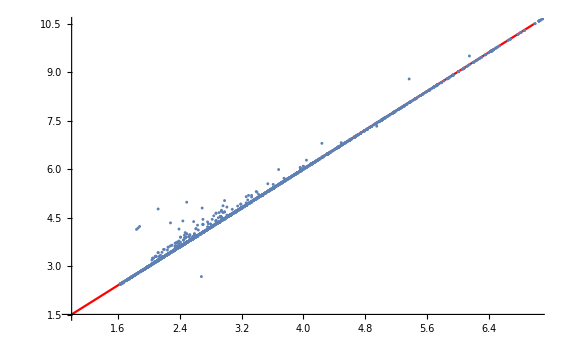

```mathematica
Show[Plot[model[x],{x,1,7},PlotStyle->Red],item[ListPlot,{"Bottle_Cost","Bottle_Retail_Price"}]]
```

```mathematica
Position[data,{_Real,_String}]
```

{{2176},{2355},{2475}}

```mathematica
item[[{2176,2355,2475}]]
```

```mathematica
Position[item[All,"Category"],""]
```

{{3},{3603},{3604},{3605}}

```mathematica
#["Item_Description"]&/@item[[{3,3603,3604,3605}]]
```

```mathematica
invoice[Counts,"Ca
```

```mathematica
Normal@%
```

{Yummy Surstromming Juice,Miku's Leek Juice,Dark Fantasy,Butterbeer}

```mathematica
item[Counts,"Category"]
```

```mathematica
Length[item]
```

4166

```mathematica
item[[19]]
```

```mathematica
item[Union,"Item_Description"]//Length
```

4166

```mathematica
item[Union,"Category"]
```

```mathematica
Length[item]
```

4166

## Observations

The cost price relationship is roughly linear as  price ~ 0.0104165+1.49998 Cost

There are 12 different categories of drink and some are not labeled into a category (Yummy Surstromming Juice, Miku’s Leek Juice, Dark Fantasy, Butterbeer)